# Numerical Simulation: Infinite Series

## Ghost-free operator acting on a bump function

· Description: We focus on calculating the infinite derivatives of a bump function on an open set between 1 and 2. The profile of the function in this interval is given by f[xv,n].

```mathematica
ClearAll[roundUp]
roundUp=Ceiling[#+1/2]&;
```

· Variable declaration

```mathematica
Clear[p];
p=2;
```

```mathematica
Clear[r,f];
r=1/2 Log[p];
f[xv_,n_]:=(-r)^n/(n!)D[Exp[-(x-1)^2/(4-x^2)],{x,2n}]/.x->xv//Simplify
```

· Values between which the function is to be evaluated

```mathematica
Clear[intsup,intinf];
intsup=1.9;
intinf=1.9;
```

```mathematica
Clear[n,ϵ];
n=3;
ϵ=0.2;
If[Abs[intsup-intinf]<ϵ,ϵ=1];
```

· Number of derivatives (n) and split (epsilon) between values

```mathematica
Clear[space,SumInf];
If[Abs[intsup-intinf]/ϵ<1,space=2,
If[Abs[intsup-intinf]/ϵ==1,space=3,
space =roundUp[Abs[intsup-intinf]/ϵ+1]
];
];
SumInf=Table[0,space,{n+2}];
index=1;
```

· Construction of the list of values.

```mathematica
For[i=1,i≤n+1,i++,SumInf[[1,i+1]]=i];
For[xj=intinf,xj <=intsup,xj+=ϵ,
SumInf[[index+1,1]]=xj;
index+=1;
];
```

· Calculation:

```mathematica
Clear[index,Sumterms,g,xj];
index=2;

For[xj=intinf,
xj≤intsup,xj+=ϵ,
Sumterms=0;
For[i=1,i≤n+1,i++,
g[xj,i-1]=f[x,i-1]/.x->xj;
Sumterms+=g[xj,i-1];
SumInf[[index,i+1]]=Sumterms;
];
index+=1;
];
```

```mathematica
SumInf//MatrixForm//N
```

(0. | 1. | 2. | 3. | 4.
1.9 | 0.125315 | -4.97997 | 1271.81 | 232685.)

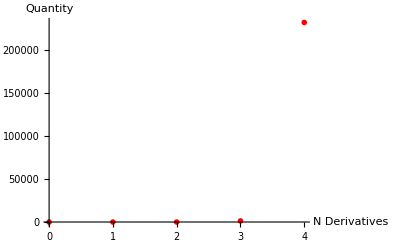

```mathematica
ListPlot[{SumInf[[1]],SumInf[[2]]}//Transpose,PlotRange->All, AxesLabel->{"N Derivatives","Quantity"},PlotTheme->"Monochrome",PlotStyle->Red]
```